Wolfram Online Mini Campus. Part 4

Instagram Posts
Pinterest Posts
"Translation" of  SageMath Online Mini Campus. Part 4

"NeuralNetwork" Method

```mathematica
train=Table[x->Sin[x]*Exp[x]+RandomVariate[NormalDistribution[0,1]],
{x,RandomReal[{-3,3},100]}];
methods={"NeuralNetwork","RandomForest","GaussianProcess"}; 
{NN,RF,GP}=Predict[train, Method->#] &/@ methods;
Show[ListPlot[List@@@train,PlotStyle->Black,PlotLegends->{"Data"}],
         Plot[{NN[x],RF[x],GP[x]},{x,-3,3},PlotLegends->methods]]
```

-Graphics-

ClassifierMeasurements with Uncertainty

```mathematica
train=ResourceData[ResourceObject["Sample Data: Wine Quality"],"TrainingData"]; 
test=ResourceData[ResourceObject["Sample Data: Wine Quality"],"TestData"];
RandomSample[train,1]
```

{{6.6,0.24,0.3,13.,0.052,18.,143.,0.99825,3.37,0.49,9.4}→6.}

```mathematica
clf=Classify[train]
```

ClassifierFunction[…]

```mathematica
el=RandomSample[test,1]
clf[el[[1,1]],"TopProbabilities"]
```

{{6.6,0.39,0.22,4.,0.038,17.,98.,0.99018,3.25,0.53,13.}→7.}

{7.→0.728214,6.→0.14287,5.→0.1011}

```mathematica
cm=ClassifierMeasurements[clf,test];
cm["Accuracy",ComputeUncertainty->True]
```

0.4580.014

CSV Files & Datasets

```mathematica
s1="https://raw.githubusercontent.com/OlgaBelitskaya/";
s2="machine_learning_engineer_nd009/master/Machine_Learning_Engineer_ND_P3/";
s3="customers.csv";
c=Import[StringJoin[s1,s2,s3],"Dataset", "HeaderLines" -> 1];
BarChart[c[1;;5,3;;8],ChartElementFunction->"GlassRectangle",
ImageSize->Large,ChartStyle->"BrightBands",
ChartLabels->Placed[Normal[Keys[c[1]][3;;8]],Axis,Rotate[#,Pi/2] &]]
```

-Graphics-

Function Derivatives

```mathematica
f[x_]=x*Exp[x]; g[x_]=1/(x+1); 
pl1=Placed[LineLegend["Expressions",LegendLayout -> {"Column",1}],Left];
pl2=Placed[LineLegend["Expressions",LegendLayout -> {"Column",1}],Right];
cols1=Table[ColorData["DarkBands"][i/9],{i,Range[0,8,1]}]; 
cols2=Table[ColorData["BrightBands"][i/9],{i,Range[0,8,1]}];
t1=Plot[Evaluate[Table[D[f[x],{x,i}],{i,Range[0,8,1]}]],
{x,-3,0},PlotStyle->cols1,PlotLegends->pl1];
t2=Plot[Evaluate[Table[D[g[x],{x,i}],{i,Range[0,8,1]}]],
{x,0,3},PlotStyle->cols2,PlotLegends->pl2];
Show[{t1,t2},PlotRange->{{-3,3},{-1,4}},ImageSize->{700,500},GridLines->Automatic]
```

-Graphics-

Polar Plots with Exclusions

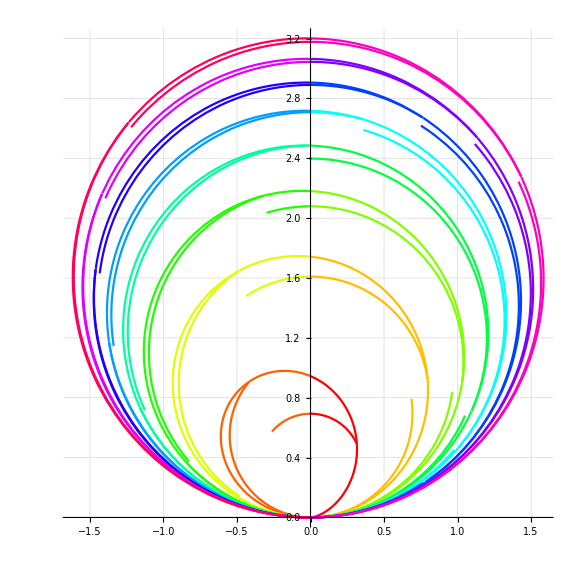

```mathematica
p=Table[PolarPlot[{Sin[x]Log[Floor[x+1]],Sin[x]Log[x+1]},
{x,k*Pi/2,(k+1)*Pi/2},
PlotStyle->Hue[k/16]],{k,Range[0,15,1]}];
Show[p,ImageSize->Large,GridLines->Automatic]
```

Sets of Surfaces

```mathematica
cp=ContourPlot3D[x^2/9+y^2/4+z^2-1==0,
{x,-3.5,3.5},{y,-3.5,3.5},{z,-3.5,3.5},
ColorFunction->(ColorData["BrightBands"][#3] &),
Mesh->False,ContourStyle->Opacity[0.8]];
sp=Table[Graphics3D[{Hue[i/24],Opacity[i/24],
Sphere[{0,3*Cos[Pi*i/12],3*Sin[Pi*i/12]},0.2]}],
{i,Range[1,24,1]}];
Show[cp,sp, Boxed->False,Axes->False,ImageSize->Large]
```

-Graphics3D-

Texts & Strings

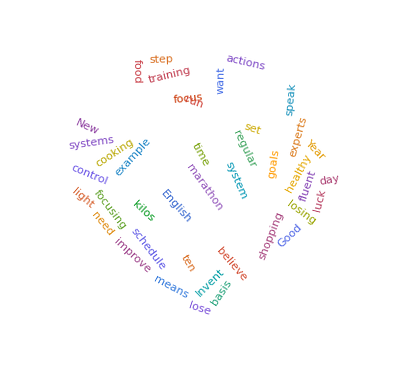

-Graphics-

```mathematica
corpus ={"Have you already set your goals for the New Year?",
"Do you want to lose ten kilos, run a marathon or speak fluent English?", 
"Some experts believe that you need systems, not goals.",
"A system is something you do on a regular basis.",
"This means focusing on what you can control (your actions) rather than what you can not.",
"For example, do not focus on losing ten kilos.",
"Focus on shopping for healthy food and cooking something light every day.",
"Do not focus on the marathon.","Focus on the training schedule.",
"Invent a system to improve your English, one step at a time.","Good luck!"};
wcorpus=StringReplace[StringJoin[corpus], PunctuationCharacter :> " "];
wc=KeySort[WordCounts[ToLowerCase[wcorpus]]]; fc= -Graphics-;
WordCloud[wcorpus,fc,WordOrientation->"Random",PlotTheme->"Web"]
BarChart[wc,ChartLabels->Placed[Normal[Keys[wc]],Axis,Rotate[#,Pi/2] &],
ChartStyle->"Pastel",ChartElementFunction->"GlassRectangle",ImageSize->600]
```

```mathematica
Sort[TextWords[wcorpus]]
```

{a,a,a,a,A,actions,already,and,at,basis,believe,can,can,control,cooking,day,do,do,Do,Do,English,English,every,example,experts,fluent,focus,focus,Focus,Focus,focusing,food,for,for,For,goals,goals,Good,Have,healthy,improve,Invent,is,kilos,kilos,light,lose,losing,luck,marathon,marathon,means,need,New,not,not,not,not,on,on,on,on,on,on,one,or,rather,regular,run,schedule,set,shopping,Some,something,something,speak,step,system,system,systems,ten,ten,than,that,the,the,the,This,time,to,to,training,want,what,what,Year,you,you,you,you,you,you,your,your,your}

```mathematica
ResourceFunction["StringFunction"][Sort][corpus[[1]]]
```

?         aaaaadeeeeeefghHllNoooorrrrssttuuvwyyyY

HTML Images

```mathematica
EmbeddedHTML["<div title='An Image Example' 
style='border:10px double white; width:156px; height:156px; overflow:auto; padding:12px; background-color:#3636ff'/>
<img src='https://olgabelitskaya.github.io/flower.png' width='150' height='150'/>"]
```

Null<div title='An Image Example' 
style…lower.png' width='150' height='150'/><div title='An Image Example' 
style='border:10px double white; width:156px; height:156px; overflow:auto; padding:12px; background-color:#3636ff'/>
<img src='https://olgabelitskaya.github.io/flower.png' width='150' height='150'/>